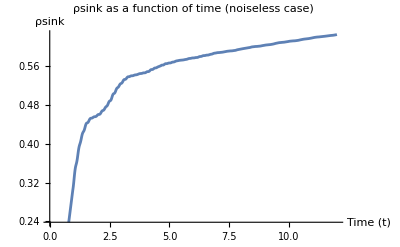

61.0801 % Population percent of the sink after 10 ps (noiseless case)

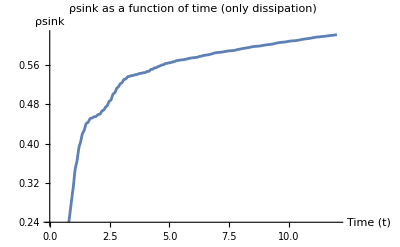

60.8785 % Population percent of the sink after 10 ps (only dissipation case)

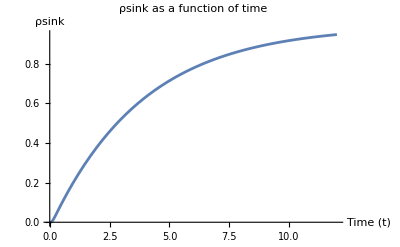

91.7433 % Population percent of the sink after 10 ps

```mathematica
(*Parameters: unity in ps^(-1)*)
Γ=10^(-3); 
Δ=(6.283);
H=(1.2414/6.58)*{{215,−104.1, 5.1,−4.3, 4.7,−15.1,−7.8,0},{−104.1, 220.0, 32.6, 7.1, 5.4, 8.3, 0.8,0},{5.1, 32.6, 0.0,−46.8, 1.0,−8.1, 5.1,0},{−4.3, 7.1,−46.8, 125.0,−70.7,−14.7,−61.5,0},{4.7, 5.4, 1.0,−70.7, 450.0, 89.7,−2.5,0},{−15.1, 8.3,−8.1,−14.7, 89.7, 330.0, 32.7,0},{−7.8, 0.8, 5.1,−61.5,−2.5, 32.7, 280.0,0},{0,0,0,0,0,0,0,0}};
γ=(1*Δ)*{0.157,9.432,7.797,9.432,7.797,0.922,9.433}; (*Note the speed (efficiency): if γ/Δ>>1 efficiency is slow *)
 (*Initial condition: single excitation in site 1*)
Init={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
(*Auxiliary matrices entering the master equation: we assume site 8 is the sink and so we deal with 8x8=64 coupled equations*)
resethp={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0}};
sinco={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0}};
au1={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
sincotr=Transpose[sinco];
gamma={{γ[[1]],0,0,0,0,0,0,0},{0,γ[[2]],0,0,0,0,0,0},{0,0,γ[[3]],0,0,0,0,0},{0,0,0,γ[[4]],0,0,0,0},{0,0,0,0,γ[[5]],0,0,0},{0,0,0,0,0,γ[[6]],0,0},{0,0,0,0,0,0,γ[[7]],0},{0,0,0,0,0,0,0,0}};
gamma1={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
gamma2={{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
gamma3={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
gamma4={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
gamma5={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
gamma6={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
gamma7={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0}};
(*Solving master equation and plot sink population as a function of time*)
(*first noiseless case*)
initialConditions={ρ[0]==Init };
system=Thread[ρ'[t]==-ⅈ(resethp.(H.ρ[t]).resethp-resethp.(ρ[t].H).resethp)-Δ*au1.ρ[t]-Δ*ρ[t].au1+2*Δ*sinco.ρ[t].sincotr];
sol=NDSolve[{system,initialConditions},ρ,{t,0,20}];
elementToPlot[t_]:=(ρ[t]/. sol)[[1]][[8,8]]; 
Plot[elementToPlot[t],{t,0,12},PlotLabel->"ρsink as a function of time (noiseless case)",AxesLabel->{"Time (t)","ρsink"}]
"Population percent of the sink after 10 ps (noiseless case)"Re[(ρ[10]/. sol)[[1]][[8,8]]]*100 "%" 
(*then with only dissipation*)
initialConditionsdiss={ρdiss[0]==Init };
systemdiss=Thread[ρdiss'[t]==-ⅈ(resethp.(H.ρdiss[t]).resethp-resethp.(ρdiss[t].H).resethp)-Δ*au1.ρdiss[t]-Δ*ρdiss[t].au1+2*Δ*sinco.ρdiss[t].sincotr-2*Γ*resethp.ρdiss[t].resethp];
sol=NDSolve[{systemdiss,initialConditionsdiss},ρdiss,{t,0,20}];
elementToPlotdiss[t_]:=(ρdiss[t]/. sol)[[1]][[8,8]];
Plot[elementToPlotdiss[t],{t,0,12},PlotLabel->"ρsink as a function of time (only dissipation)",AxesLabel->{"Time (t)","ρsink"}]
"Population percent of the sink after 10 ps (only dissipation case)"Re[(ρdiss[10]/. sol)[[1]][[8,8]]]*100 "%" 
(*then with dissipation and dephasing*)
initialConditionsnoise={ρn[0]==Init };
systemnoise=Thread[ρn'[t]==-ⅈ(resethp.(H.ρn[t]).resethp-resethp.(ρn[t].H).resethp)-Δ*au1.ρn[t]-Δ*ρn[t].au1+2*Δ*sinco.ρn[t].sincotr-2*Γ*resethp.ρn[t].resethp-gamma.ρn[t].resethp-resethp.ρn[t].gamma+2*γ[[1]]*gamma1.ρn[t].gamma1+2*γ[[2]]*gamma2.ρn[t].gamma2+2*γ[[3]]*gamma3.ρn[t].gamma3+2*γ[[4]]*gamma4.ρn[t].gamma4+2*γ[[5]]*gamma5.ρn[t].gamma5+2*γ[[6]]*gamma6.ρn[t].gamma6+2*γ[[7]]*gamma7.ρn[t].gamma7];
sol=NDSolve[{systemnoise,initialConditionsnoise},ρn,{t,0,20}];
elementToPlotn[t_]:=(ρn[t]/. sol)[[1]][[8,8]];
Plot[elementToPlotn[t],{t,0,12},PlotLabel->"ρsink as a function of time",AxesLabel->{"Time (t)","ρsink"}]
"Population percent of the sink after 10 ps"Re[(ρn[10]/. sol)[[1]][[8,8]]]*100 "%" (*Population percent of the sink after 10 ps (efficiency)*)
```